```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

### Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,len_]:=Module[{temp=Range[1,len],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,len}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Snnscan/results/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Snnscan/results/"<>temp<>".dat",res];];

import[res_]:=res=Import["spectraldata/Snnscan/results/"<>ToString[res]<>".dat"];
```

## Snn Scan

```mathematica
(* s here is √Subscript[s, NN] in GeV*)
T[s_]:=Tlim 1/(1+Exp[1.72-Log[s/0.45]]);
μ[s_]:=(1303 10^-3)/(1+0.286 s);
Tlim=0.155;
```

```mathematica
Tmuscan=Join[Table[{i,T[i],μ[i]},{i,8,195,10}],Table[{i,T[i],μ[i]},{i,200,1000,100}],Table[{i,T[i],μ[i]},{i,2000,10000,1000}]]
```

{{8,0.117949,0.39629},{18,0.136011,0.211939},{28,0.142234,0.144649},{38,0.145385,0.109791},{48,0.147289,0.0884709},{58,0.148563,0.0740846},{68,0.149476,0.0637226},{78,0.150162,0.0559036},{88,0.150697,0.0497936},{98,0.151125,0.0448877},{108,0.151475,0.0408618},{118,0.151768,0.0374986},{128,0.152015,0.0346469},{138,0.152228,0.0321983},{148,0.152412,0.0300729},{158,0.152573,0.0282108},{168,0.152716,0.0265658},{178,0.152842,0.0251021},{188,0.152955,0.0237913},{200,0.153077,0.0223883},{300,0.153712,0.0150115},{400,0.154032,0.0112912},{500,0.154225,0.00904861},{600,0.154354,0.00754925},{700,0.154446,0.00647614},{800,0.154515,0.00567015},{900,0.154568,0.00504257},{1000,0.154611,0.00454007},{2000,0.154805,0.002274},{3000,0.15487,0.00151688},{4000,0.154903,0.00113799},{5000,0.154922,0.000910552},{6000,0.154935,0.000758882},{7000,0.154944,0.000650524},{8000,0.154951,0.000569244},{9000,0.154957,0.000506019},{10000,0.154961,0.000455435}}

```mathematica
Do[ccdata[n]=Import["spectraldata/Snnscan/cc/swccs"<>ToString[Tmuscan[[n,1]]]<>"spectra.dat"];,{n,Length[Tmuscan]}];
Do[ccdatau[n]=Import["spectraldata/Snnscan/cc/swccs"<>ToString[Tmuscan[[n,1]]]<>"uspectra.dat"];,{n,Length[Tmuscan]}];
Do[ccdatal[n]=Import["spectraldata/Snnscan/cc/swccs"<>ToString[Tmuscan[[n,1]]]<>"lspectra.dat"];,{n,Length[Tmuscan]}];
```

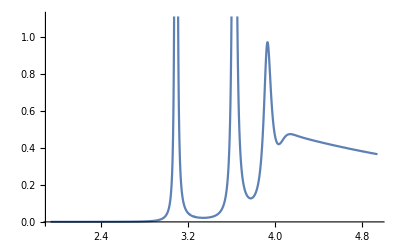

```mathematica
ListPlot[ccdatal[6],Joined->True]
```

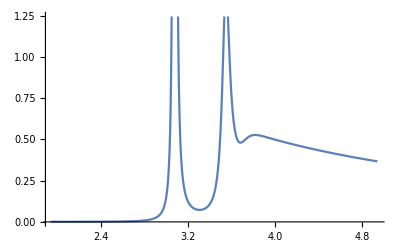

```mathematica
ListPlot[ccdata[6],Joined->True]
```

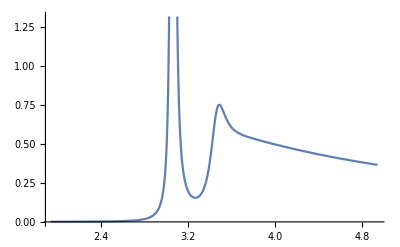

```mathematica
ListPlot[ccdatau[6],Joined->True]
```

### Perform Fitting

```mathematica
Clear[ccmodel,ccmodell,ccmodelu]
fitnew[ccdata,ccmodel,Length[Tmuscan]];
fitnew[ccdatau,ccmodelu,Length[Tmuscan]];
fitnew[ccdatal,ccmodell,Length[Tmuscan]];
```

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];,{i,Length[ccmodel]}];
Do[If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];,{i,Length[ccmodelu]}];
Do[If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodell]}];
```

```mathematica
Clear[wrfitcc,gfitcc,areafitcc,cfitcc,dfitcc,sfitcc,s2fitcc,wrfitccu,gfitccu,areafitccu,cfitccu,dfitccu,sfitccu,s2fitccu,wrfitccl,gfitccl,areafitccl,cfitccl,dfitccl,sfitccl,s2fitccl];
store[wr,wrfitcc,ccmodel];
store[Γ,gfitcc,ccmodel];
store[const,cfitcc,ccmodel];
store[δbg,dfitcc,ccmodel];
store[shift,sfitcc,ccmodel];
store[shift2,s2fitcc,ccmodel];
storearea[areafitcc,ccmodel];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitccu,ccmodelu];
store[const,cfitccu,ccmodelu];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitccu,ccmodelu];
store[wr,wrfitccl,ccmodell];
store[Γ,gfitccl,ccmodell];
store[const,cfitccl,ccmodell];
store[δbg,dfitccl,ccmodell];
store[shift,sfitccl,ccmodell];
store[shift2,s2fitccl,ccmodell];
storearea[areafitccl,ccmodell];
```

### Import previous results

```mathematica
import[wrfitcc];
import[gfitcc];
import[cfitcc];
import[dfitcc];
import[sfitcc];
import[s2fitcc];
import[areafitcc];
import[wrfitccu];
import[gfitccu];
import[cfitccu];
import[dfitccu];
import[sfitccu];
import[s2fitccu];
import[areafitccu];
import[wrfitccl];
import[gfitccl];
import[cfitccl];
import[dfitccl];
import[sfitccl];
import[s2fitccl];
import[areafitccl];
```

### View results

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitcc],1},{ii,1,Length[wrfitcc[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccu],1},{ii,1,Length[wrfitccu[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccl],1},{ii,1,Length[wrfitccl[[1]]],1}]
```

### DiLetpon Ratio

```mathematica
Emfactor=2.356305815440891;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0=ConstantArray[0,Length[wrfitcc]];
Do[If[Length[wrfitcc[[ii]]]==2,R0[[ii]]={Tmuscan[[ii,1]],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tmuscan[[ii,2]]])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tmuscan[[ii,2]]])}],{ii,Length[R0]}];
R0u=ConstantArray[0,Length[wrfitccu]];
Do[If[Length[wrfitccu[[ii]]]==2,R0u[[ii]]={Tmuscan[[ii,1]],Emfactor (areafitccu[[ii,2]]nB[wrfitccu[[ii,2]],Tmuscan[[ii,2]]])/(areafitccu[[ii,1]]nB[wrfitccu[[ii,1]],Tmuscan[[ii,2]]])}],{ii,Length[R0u]}];
R0l=ConstantArray[0,Length[wrfitccl]];
Do[If[Length[wrfitccl[[ii]]]==2,R0l[[ii]]={Tmuscan[[ii,1]],Emfactor (areafitccl[[ii,2]]nB[wrfitccl[[ii,2]],Tmuscan[[ii,2]]])/(areafitccl[[ii,1]]nB[wrfitccl[[ii,1]],Tmuscan[[ii,2]]])}],{ii,Length[R0l]}];
```

```mathematica
R0=DeleteCases[R0,0];
R0u=DeleteCases[R0u,0];
R0l=DeleteCases[R0l,0];
```

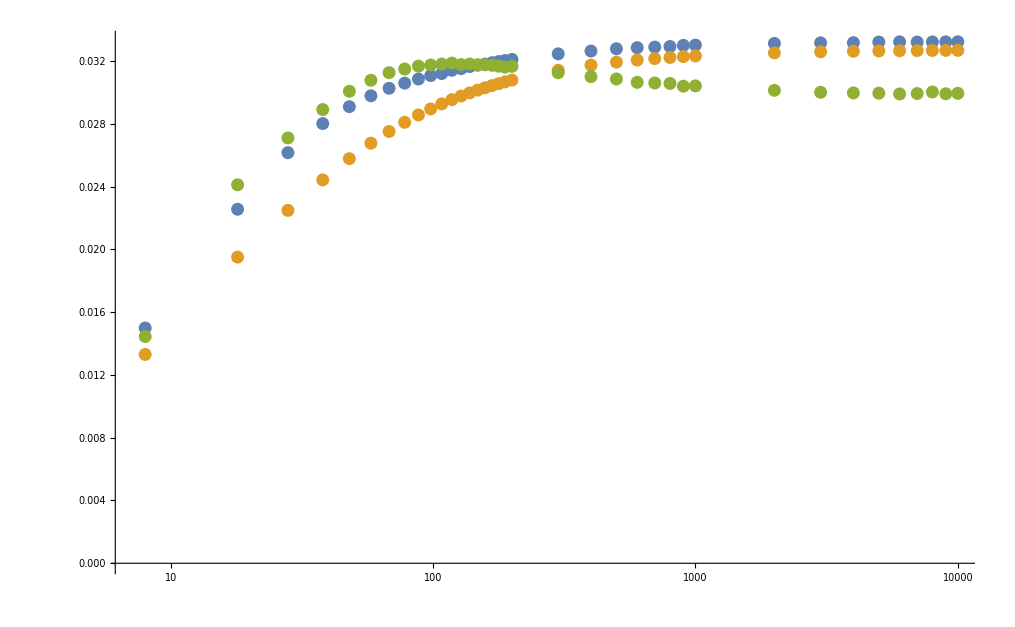

```mathematica
ListLogLinearPlot[{R0,R0l,R0u},PlotRange->All]
```

```mathematica
.
```

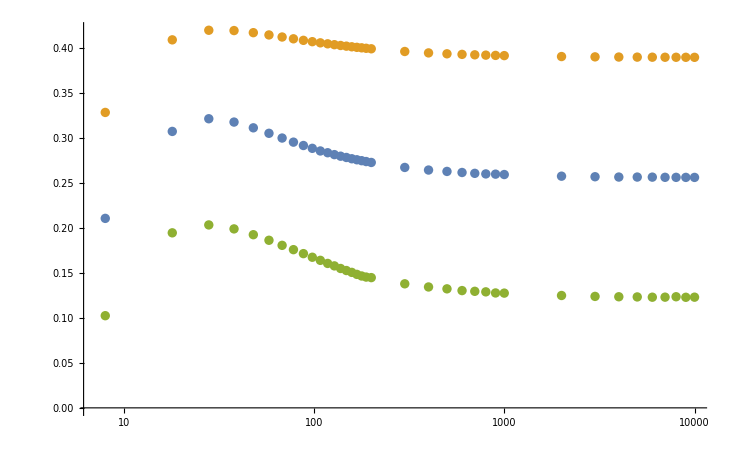

```mathematica
ListLogLinearPlot[{Table[{Tmuscan[[ii,1]],areafitcc[[ii,2]]/areafitcc[[ii,1]]},{ii,1,Length[areafitccu]}],Table[{Tmuscan[[ii,1]],areafitccl[[ii,2]]/areafitccl[[ii,1]]},{ii,1,Length[areafitccl]}],Table[{Tmuscan[[ii,1]],areafitccu[[ii,2]]/areafitccu[[ii,1]]},{ii,1,Length[areafitccu]}]},PlotRange->All]
```

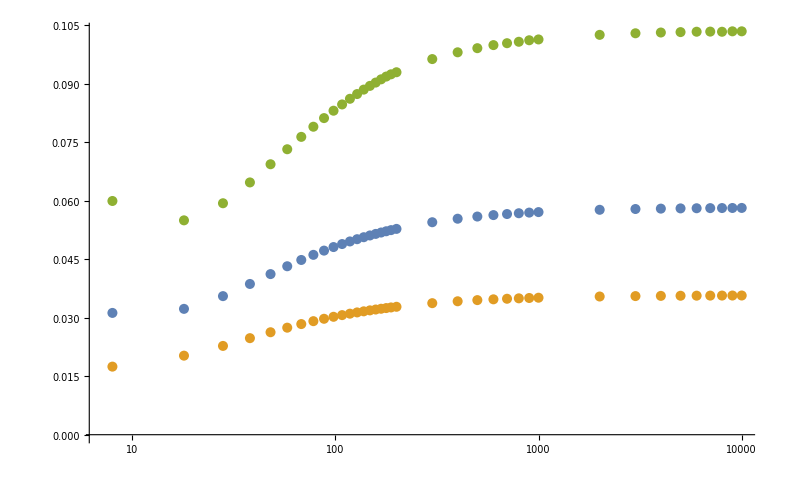

```mathematica
ListLogLinearPlot[{Table[{Tmuscan[[ii,1]],nB[wrfitcc[[ii,2]],Tmuscan[[ii,2]]]/nB[wrfitcc[[ii,1]],Tmuscan[[ii,2]]]},{ii,1,Length[areafitccu]}],Table[{Tmuscan[[ii,1]],nB[wrfitccl[[ii,2]],Tmuscan[[ii,2]]]/nB[wrfitccl[[ii,1]],Tmuscan[[ii,2]]]},{ii,1,Length[areafitccu]}],Table[{Tmuscan[[ii,1]],nB[wrfitccu[[ii,2]],Tmuscan[[ii,2]]]/nB[wrfitccu[[ii,1]],Tmuscan[[ii,2]]]},{ii,1,Length[areafitccl]}]},PlotRange->All]
```

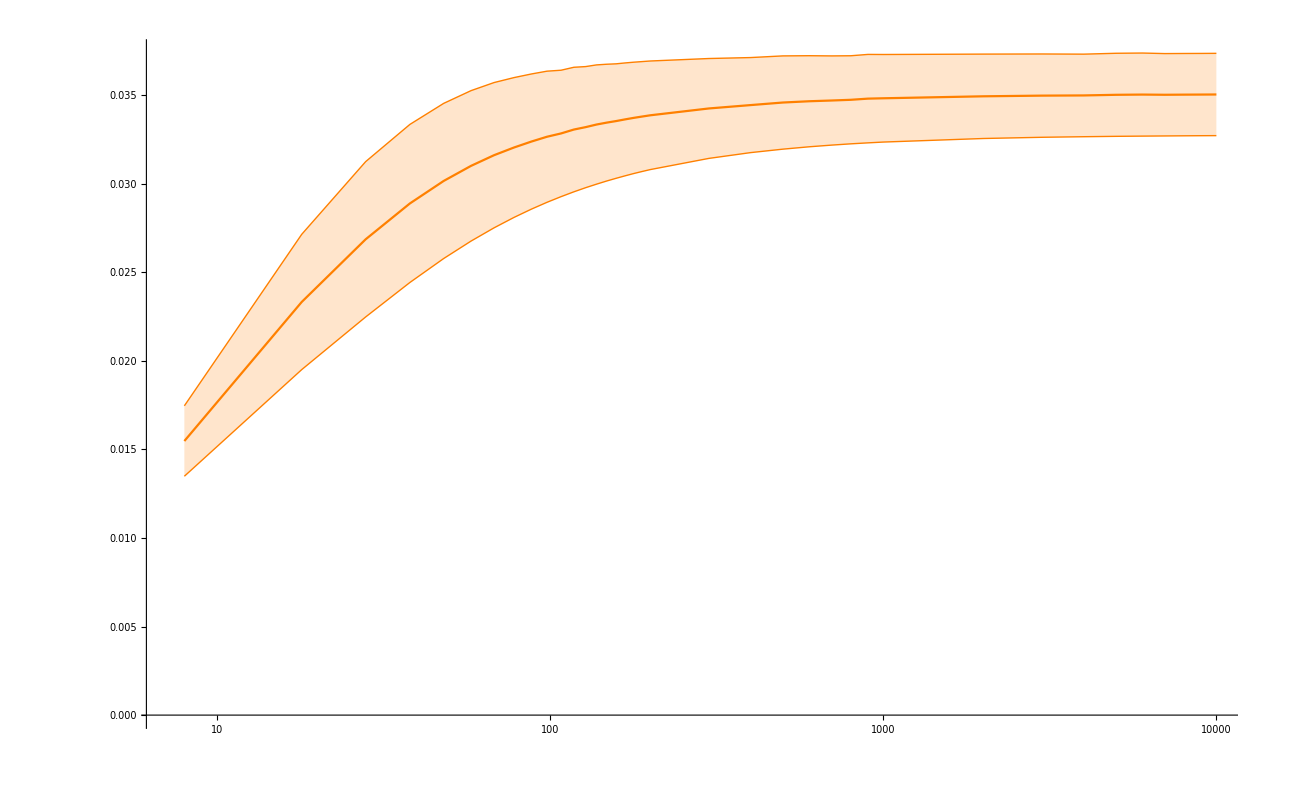

```mathematica
ListLogLinearPlot[{R0,R0l,R0+(R0-R0l)},PlotRange->All,Joined->True,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2],PlotStyle->{Orange,{Orange,Thin},{Orange,Thin}}]
```